{{x→InterpolatingFunction[{{0., 10.}}, <>]}}

Relativistic Simple Harmonic Motion:

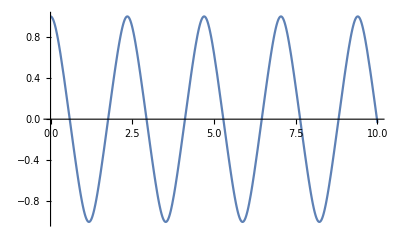

```mathematica
m=1;
ω=Pi;
A=1;
c=Pi;
T=10;
L=-m*c^2*Sqrt[1-x'[t]^2/c^2]-m/2*ω^2*x[t]^2;
Needs["VariationalMethods`"]
eqs=EulerEquations[L,x[t],t];
s=NDSolve[{eqs,x[0]==A,x'[0]==0},x,{t,0,T}]

"Relativistic Simple Harmonic Motion:"
Plot[Evaluate[{x[t]}/.s],{t,0,T}]
plt=Plot[-50,{x,-A-0.1,A+0.1},PlotRange->{-0.1,0.1},Axes->{True,False}];
Animate[Show[plt,Graphics[{Blue,Ball[{x[t],0},1/32]}],AspectRatio->Automatic]/.s,{t,0,T},AnimationRate->1, AnimationRunning->False,RefreshRate->300]
```